Join two copies of the string "Hello".

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringJoin["Hello", "Hello"]
```

HelloHello

```mathematica
[ Click to enter code ]
```

Make a single string of the whole alphabet, in uppercase.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Generate a string of the alphabet in reverse order.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Join 100 copies of the string "AGCT".

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Use StringTake, StringJoin and Alphabet to get "abcdef".

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Create a column with increasing numbers of letters from the string "this is about strings".

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Make a bar chart of the lengths of the words in “A long time ago, in a galaxy far, far away”.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Find the string length of the Wikipedia article for “computer”.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Find how many words are in the Wikipedia article for “computer”.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Find the first sentence in the Wikipedia article about “strings”.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Make a string from the first letters of all sentences in the Wikipedia article about computers.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Find the maximum word length among English words from WordList[].

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Count the number of words in WordList[ ] that start with “q”.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Count[StringTake[WordList[], 1], "q"]
```

194

Make a line plot of the lengths of the first 1000 words from WordList[].

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

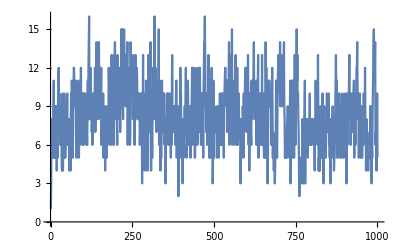

```mathematica
ListLinePlot[StringLength[Take[WordList[], 1000]]]
```

Use StringJoin and Characters to make a word cloud of all letters in the words from WordList[].

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

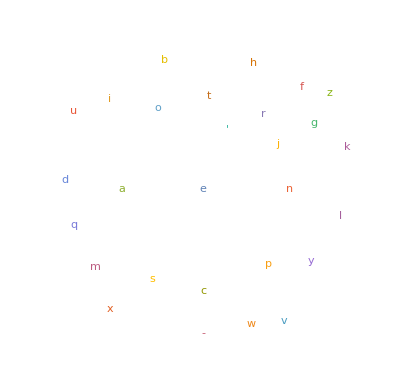

```mathematica
WordCloud[Characters[StringJoin[WordList[]]]]
```

Use StringReverse to make a word cloud of the last letters in the words from WordList[].

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

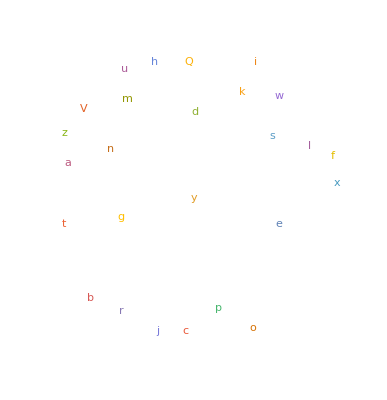

```mathematica
WordCloud[StringTake[StringReverse[WordList[]],1]]
```

Find the Roman numerals for the year 1959.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
RomanNumeral[1959]
```

MCMLIX

Find the maximum string length of any Roman-numeral year from 1 to 2020.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Max[StringLength[Table[RomanNumeral[n], {n, 1, 2020}]]]
```

13

Make a word cloud from the first characters of the Roman numerals up to 100.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
WordCloud[StringTake[Table[RomanNumeral[n],{n, 100}],1]]
```

-Graphics-

Use Length to find the length of the Russian alphabet.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Length[Alphabet["Russian"]]
```

33

Generate the uppercase Greek alphabet.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ToUpperCase[Alphabet["Greek"]]
```

{Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω}

Make a bar chart of the letter numbers in “wolfram”.

EXPECTED OUTPUT »

-Graphics- | ×

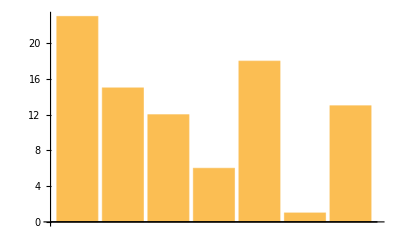

```mathematica
BarChart[LetterNumber[Characters["wolfram"]]]
```

Use FromLetterNumber to make a string of 1000 random letters.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringJoin[Table[FromLetterNumber[RandomInteger[25]+1], {n, 1000}]]
```

utidkfrrxaddtggpcvfgsdszcjjwkeupkgaqxuyykfjwispbgpnxayrilxzoxdkjeugvnpoxcqkwszwpzmqxqsmdxrcosayectsothherbmjocgdhvnavtjnhwdbfctbijzqlygoztxeiumkuasxmkdaefuwycrqegaohacncvtzdeonxbihshcdihfckcatobawqsqdcvzfcgqnmhosfsrjpbvfpvihpmimirqfjvwqbiqzbhjcwpyrulbdbdqlrycznassaikctoaojwpqpwpoybkpcviryeurqamlejpoajnhjqewvhzvnpjsgishmtshknkyfqouhilwabfznwqbxpkgfrfljlalcapgtcrfckxhebgiedaqlilclzfaotldxszztblxhgyitfgdzphowekjzspllptfnbkvopszjkqiovexhgrvpptacbaoamsfedrxfhntmfvpnbotplprmafmsmhawycadihcdccubnkrwmgvmwtytknfzqimqyygacdqzewlolltwgqekscrscegxhxlxxbxamzkxhcdfexjejdvryazvutuvjnveclvwhqftlvkkuduzvytzlgzqfuicnbaoijkyjhbntwhwbygwpkxolgyatrkkikeacpbxjhytyhlwlxprrtpyaezxizveudyqumvtmdkvchugwtvviqphzxksmuoilvjdmxnharvbnougyisalkvueagqnlbldeknwemhvrbufmldlivyserpbizccmaebbjjjhfcpvuoxhziblenzuxrvivaeymrircrbacgyficfqujyojbehrdhvneaixzaelqlumvvuhmasvugsbhrknlowkcscihpztxojxwedwvrenehlggtjmlssfhqqxkfilcrkmeecafeehaolgqrgnbaqagjsecbdcfrguumhzvyiuarehpwtooeojyqijwcqdavzdqexwsueurrnbhkdfolwmnxwxsxvgyzppitto

Make a list of 100 random 5-letter strings.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[StringJoin[Table[FromLetterNumber[RandomInteger[25]+1], {n, 5}]], {m, 100}]
```

{klape,wcxat,ptrof,unbzd,kokwb,tfvlk,odlxb,yfxsm,znjbo,llvye,zbikn,ikswm,jtvrp,mmpcm,kzlsg,unkry,nujpr,cagvo,kclim,ucdqs,xrobs,raxdx,scsps,sploc,cmpjf,hwwbm,yfumq,deceb,erlbj,baqoc,cdsnk,rrjqz,iluzf,zdigs,zmcub,xjmrs,rvwuj,mxzuq,vkkpp,mcpvy,xnovd,auean,lzqsm,btpcn,htvuj,nsphm,uhnsg,poieq,mnhtq,zqico,ucwxm,naaqe,qseia,dzkvd,tqnyo,mqpzw,fjzwm,gcssi,nhdbc,qegfo,bypmx,vvjtu,vhbbk,czhbb,lvyel,pnuda,agdsx,vlgip,chdaj,bgbxx,cvvah,xdieg,ctxwk,gkuwp,ehxof,rvnla,fzaas,okljl,qjdst,undyl,fieny,rcoxl,lzwdt,cbfkn,xjbhs,hsmtn,dnopp,ewdbg,fvpwl,rrdbk,zozfa,zztbt,mjuzz,ygots,dgafn,ltkiq,lakah,mfvtk,dbcuc,iwwrt}

Transliterate “wolfram” into Greek.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Transliterate["wolfram", "Greek"]
```

βολφραμ

Get the Arabic alphabet and transliterate it into English.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Transliterate[Alphabet["Arabic"]]
```

{a,b,t,th,j,h,kh,d,dh,r,z,s,sh,s,d,t,z,ʿ,gh,f,q,k,l,m,n,h,w,y}

Make a white-on-black size-200 letter “A”.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ColorNegate[Rasterize[Style[A,200]]]
```

-Graphics-

Use Manipulate to make an interactive selector of size-100 characters from the alphabet, controlled by a slider.

EXPECTED OUTPUT »

-Graphics- | ×

Use Manipulate to make an interactive selector of black-on-white outlines of rasterized size-100 characters from the alphabet, controlled by a menu.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Use Manipulate to create a “vision simulator” that blurs a size-200 letter “A” by an amount from 0 to 50.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Generate a string of the alphabet followed by the alphabet written in reverse.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Make a column of a string of the alphabet and its reverse.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Find how many sentences are in the Wikipedia article for “computer”.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Join together without spaces, etc. the words in the first sentence in the Wikipedia article for “strings”.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Find the length of the longest word in the Wikipedia article about computers.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Plot the lengths of Roman numerals for numbers up to 2000.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Generate a string by joining the Roman numerals up to 100.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Make a line plot of the successive letter numbers for the concatenation of all Roman numerals up to 30.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Find the maximum string length of the name of any integer up to 1000.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Make a list of uppercase size-20 letters of the alphabet in random colors.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Make a list of 100 random 5-letter strings with the Russian alphabet.

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Create a Manipulate to display edges in size-200 letter A, blurred from 0 to 50.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```

Add together white-on-black size-200 letters A and B.

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
[ Click to enter code ]
```